```mathematica
rel[r_] := Integrate[Integrate[Cos[x+t]*Cos[r*x],{x,0,2*Pi}],{t,0,2*Pi}]
```

```mathematica
rel2[r_] := Integrate[Integrate[Cos[x+t]*Cos[r*x],{x,0,2*Pi}]^2,{t,0,2*Pi}]
```

```mathematica
Plot[rel2[r],{r,1,10}]
```

$Aborted

```mathematica
inner[ r_]:=Integrate[r,{x,-Pi,Pi}]
?inner
```

Global`inner

inner[r_]:=∫_-π^π rⅆx
 
inner[t_,r_]:=∫_0^(2 π) Cos[r x] Cos[x]ⅆx

```mathematica
Integrate[Cos[x+t]*Cos[r*x],{x,0,2*Pi}]
```

```mathematica
(r Cos[t] Sin[2 π r]+2 Sin[π r]^2 Sin[t])/(-1+r^2)
inner[r_,t_]:=(r Cos[t] Sin[2 π r]+2 Sin[π r]^2 Sin[t])/(-1+r^2)
```

(r Cos[t] Sin[2 π r]+2 Sin[π r]^2 Sin[t])/(-1+r^2)

```mathematica
Integrate[inner[r,t]^2,{t,0,2Pi}]
```

(2 π (1+r^2+(-1+r^2) Cos[2 π r]) Sin[π r]^2)/((-1+r^2)^2)

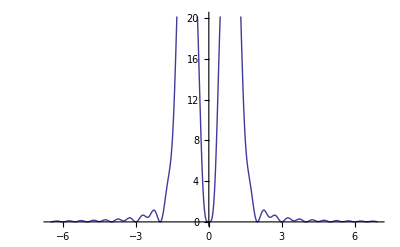

```mathematica
Plot[(2 π (1+r^2+(-1+r^2) Cos[2 π r]) Sin[π r]^2)/((-1+r^2)^2),{r,-6.508595835855094,6.934711311325067}]
```